```mathematica
Clear["Global`*"]
dx=300;
eV=1.60217657*^-12;(*erg*)
dm13=2.43*^-3*eV*eV;
M=1*^6;
Eexp=14;(*eV*)
c2=8.98755*^20;(*cm2/s2*)
epsilon =dm13/(2*Eexp);
ex4=3.06375889*^-11;ex3=-8.68941465*^-5;ex2= 2.09465957*^3;ex1=-2.12383465*^9;ex0=-2.32184538*^17;
ax4=2.12109307*^-11;ax3=-1.47767192*^-4 ;ax2=7.18777361*^3;ax1=-1.50492478*^11;ax0= 1.28967597*^18;
const:=1*^24;
fe[x_]:=const/(ex4*((dx+x)*1*^5)^4+ex3*((dx+x)*1*^5)^3+ex2*((dx+x)*1*^5)^2+ex1*((dx+x)*1*^5)^1+ex0);
fa[x_]:=const/(ax4*((dx+x)*1*^5)^4+ax3*((dx+x)*1*^5)^3+ax2*((dx+x)*1*^5)^2+ax1*((dx+x)*1*^5)^1+ax0);
vx3=-1.43989474*^-42 ;vx2=6.25000000*^-21;vx1=-1.25000000*^-14;vx0= 6.25000000*^-9;
rho[x_]:=const*6*^-26/(vx3*((dx+x)*1*^5)^3+vx2*((dx+x)*1*^5)^2+vx1*((dx+x)*1*^5)^1+vx0);
```

Null^3

```mathematica
θ:=0.15;(*13 Mixing angle*)
V:={Sin[2θ],0,Cos[2θ]};
Ve[x_]:=rho[x];
Vmatt[x_]:={0,0,Ve[x]};
Hnn[x_]:= fe[x];
nu:=1;
nubar[x_]:=fa[x]/fe[x];
tmin :=0;
tmax:=650;
```

Null^2

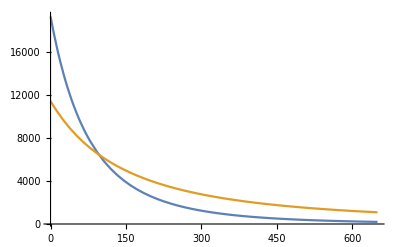

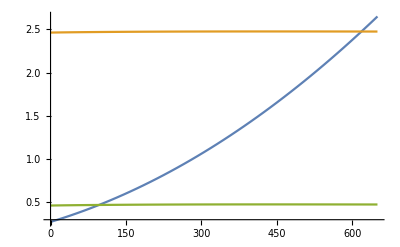

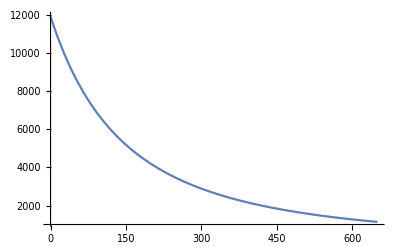

```mathematica
Plot[{fa[x]-fe[x],Ve[x]},{x,tmin,tmax},PlotRange->All]
Plot[{Ve[x]/Hnn[x],nubar[x]+1,nubar[x]-1},{x,tmin,tmax},PlotRange->All]
Plot[{Vmatt[x][[3]]/V[[3]]},{x,tmin,tmax},PlotRange->All]
```

```mathematica
Timing[sol=NDSolve[{M1'[t]==Cross[M1[t],-V+Vmatt[t]]+Hnn[t]*Cross[M1[t],M2[t]],M2'[t]==Cross[M2[t],+V+Vmatt[t]]+Hnn[t]*Cross[M2[t],M1[t]],M1[tmin]=={0,0,nu },M2[tmin]=={0,0,-nubar[tmin] }},{M1,M2},{t,tmin,tmax},MaxSteps->10000000]]
```

{69.7767,{{M1→InterpolatingFunction[{{0., 650.}}, <>],M2→InterpolatingFunction[{{0., 650.}}, <>]}}}

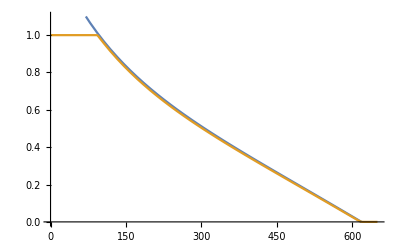

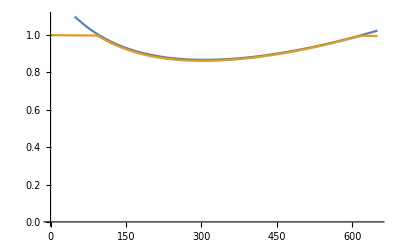

```mathematica
Pana[t_]:=(1 + ((nubar[t]^2 -1) - (Ve[t]/Hnn[t])^2)/(2*Ve[t]/Hnn[t]))/2
Panab[t_]:=(1 + ((nubar[t]^2 -1) + (Ve[t]/Hnn[t])^2)/(2*Ve[t]*nubar[t]/Hnn[t]))/2
Plot[{Pana[t],(1+(M1[t]/.sol)[[1,3]]/nu)/2},{t,tmin,tmax},PlotRange -> {{tmin,tmax},{0,1.1}}]

Plot[{Panab[t],(1-(M2[t]/.sol)[[1,3]]/nubar[t])/2},{t,tmin,tmax},PlotRange -> {{tmin,tmax},{0,1.1}}]
```